```mathematica
以下是量子围栏的程序
```

```mathematica
两种贝塞尔函数在0点的行为
```

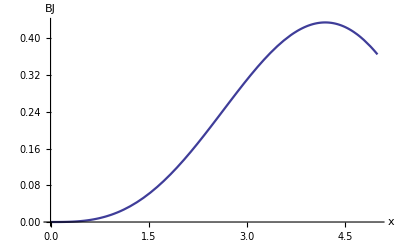

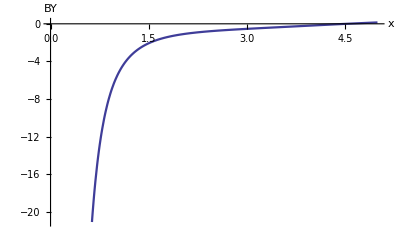

```mathematica
Plot[BesselJ[3,x],{x,0,5},AxesLabel->{"x","BJ"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[BesselY[3,x],{x,0,5},AxesLabel->{"x","BY"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```

```mathematica
观察0点情况
```

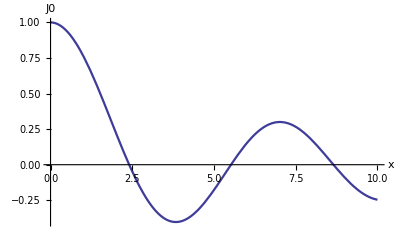

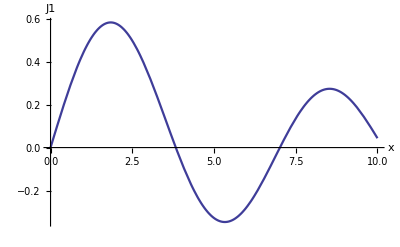

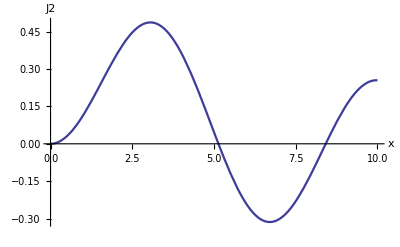

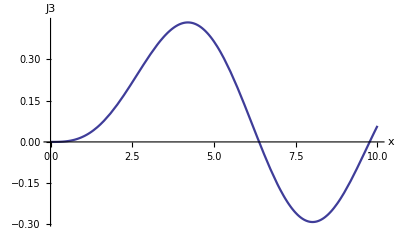

```mathematica
Plot[BesselJ[0,x],{x,0,10},AxesLabel->{"x","J0"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[BesselJ[1,x],{x,0,10},AxesLabel->{"x","J1"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[BesselJ[2,x],{x,0,10},AxesLabel->{"x","J2"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[BesselJ[3,x],{x,0,10},AxesLabel->{"x","J3"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```

```mathematica
求0阶贝塞尔的根
```

```mathematica
FindRoot[BesselJ[0,x],{x,2.4}]
FindRoot[BesselJ[0,x],{x,5.5}]
FindRoot[BesselJ[0,x],{x,8.6}]
```

{x→2.40483}

{x→5.52008}

{x→8.65373}

```mathematica
考察修正贝塞尔函数的性质
```

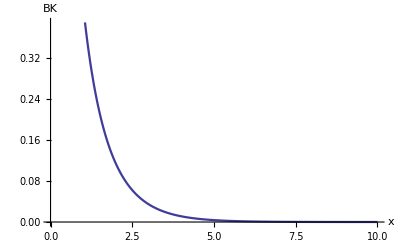

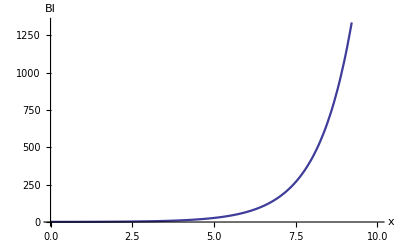

```mathematica
Plot[BesselK[0,x],{x,0,10},AxesLabel->{"x","BK"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[BesselI[0,x],{x,0,10},AxesLabel->{"x","BI"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
```

```mathematica
观察有限深围栏的解
```

-(5.11972 √x BesselJ[1,5.11972 √x])/BesselJ[0,5.11972 √x]+(5.11972 √(30-x) BesselK[1,5.11972 √(30-x)])/BesselK[0,5.11972 √(30-x)]

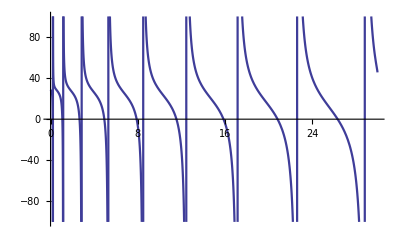

```mathematica
b=0.511972;V0=30;a=10;
diff[x_]:=
((x*D[BesselJ[0,x],x])/BesselJ[0,x]/.x->(b*√x*a))-
((x*D[BesselK[0,x],x])/BesselK[0,x]/.x->(b*√(V0-x)*a));
diff[x]
Plot[Evaluate[diff[x]],{x,0,V0},
PlotPoints->200,PlotRange->100,
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[b,V0,a,diff]
```

```mathematica
求0点的位置
```

```mathematica
b=0.511972;V0=30;a=10;result={};
diff[x_]:=
Evaluate[
((x*D[BesselJ[0,x],x])/BesselJ[0,x]/.x->(b*√x*a))-
((x*D[BesselK[0,x],x])/BesselK[0,x]/.x->(b*√(V0-x)*a))];
app={0.2,1.1,2.6,5.0,7.9,11.6,16,20.8,26};
Do[c=FindRoot[diff[x],{x,app[[i]]}];
AppendTo[result,x/.c[[1]]],{i,Length[app]}]
Partition[result,3]//TableForm
Clear[a,b,c,V0,diff,result,app]
```

0.205686 | 1.08337 | 2.66083
4.93542 | 7.90217 | 11.5527
15.8724 | 20.8317 | 26.3465

```mathematica
0阶的各个能级对应的波函数
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

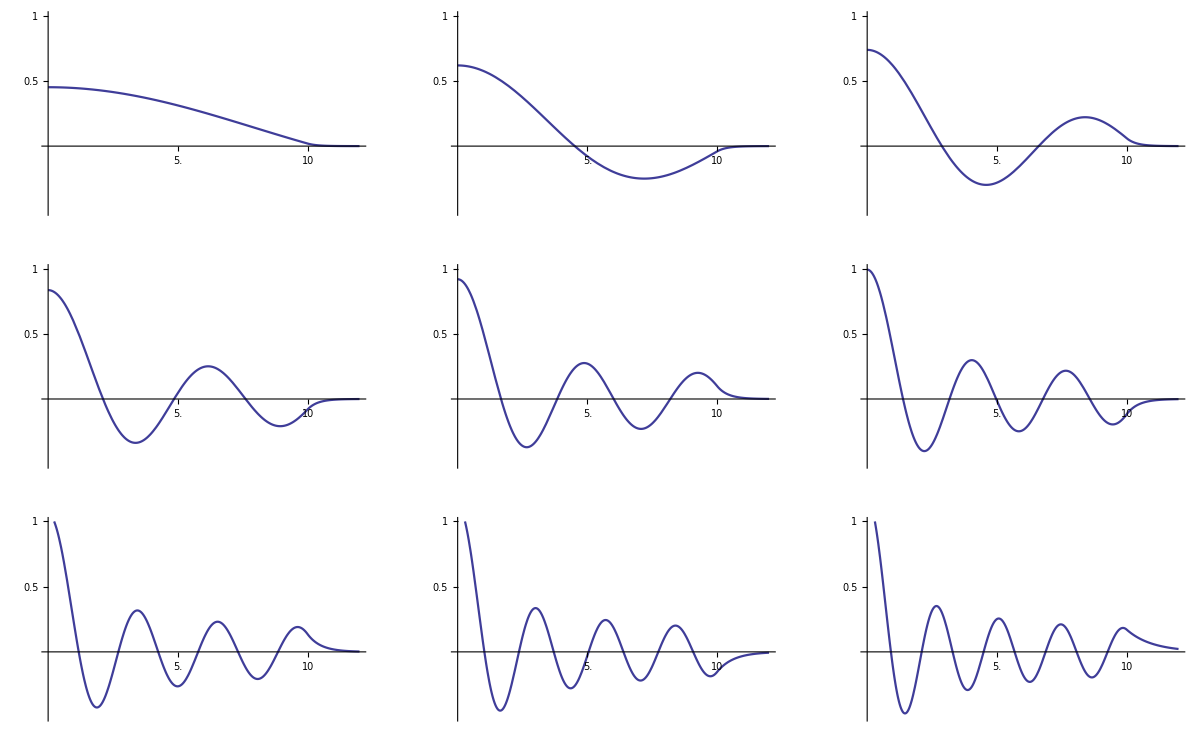

```mathematica
b=0.511972;V0=30;a=10;c2c1={};fig={};
e={0.205686,1.08337,2.66083,4.93542,7.90217,
11.5527,15.8724,20.8317,26.3465};
len=Length[e];
Do[k=(BesselJ[0,x]/.x->(b*√e[[i]]*a))/
(BesselK[0,x]/.x->(b*√(V0-e[[i]])*a));
AppendTo[c2c1,k],{i,len}]
Array[φ,len];
Do[φ[i][r_]:=If[r<a,BesselJ[0,b √e[[i]] r],
c2c1[[i]] BesselK[0,b*√(V0-e[[i]]) r]],{i,len}]
Do[ma=NIntegrate[(φ[i][r])^2,{r,0,1.2a}];
g=Plot[φ[i][r]/√ma,{r,0,1.2a},
PlotRange->{-0.5,1},Ticks->{{0.5a,a},{0.5,1}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]];
AppendTo[fig,g],{i,len}]
fig=Partition[fig,3];
Show[GraphicsArray[fig]]
Clear[a,b,e,V0,c2c1,len,k,φ,g,fig,ma]
```

```mathematica
计算0阶的所有9个波函数
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

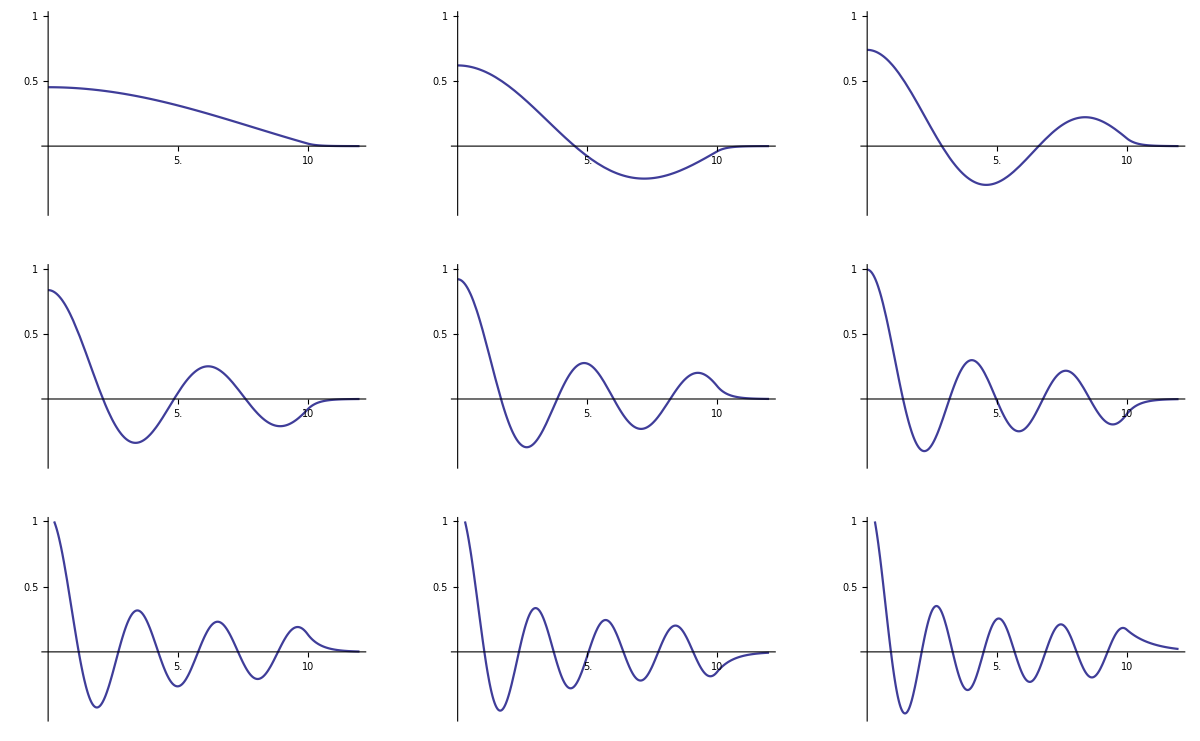

```mathematica
V0=30;a=10;d=0.262116;fig={};
e={0.205686,1.08337,2.66083,4.93542,7.90217,
11.5527,15.8724,20.8317,26.3465};
len=Length[e];
Do[
β[r_]:=d*r^2*If[r<a,-e[[i]],V0-e[[i]]];
equ={r^2*φ''[r]+r*φ'[r]-β[r]*φ[r]==0,
φ[10^-6]==1,φ'[10^-6]==0};
s=NDSolve[equ,φ,{r,10^-6,1.2a}];φ=φ/.s[[1]];
ma=NIntegrate[φ[r]^2,{r,10^-6,1.2a}];
g=Plot[φ[r]/√ma,{r,10^-6,1.2a},
PlotRange->{-0.5,1},Ticks->{{0.5a,a},{0.5,1}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]];
AppendTo[fig,g];Clear[φ],{i,len}]
fig=Partition[fig,3];
Show[GraphicsArray[fig]]
Clear[d,a,V0,e,β,equ,φ,ma,len,s,fig,g]
```